```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,δ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -δ*(ρ*H[t] + β*F[t])*R[t] ,
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
```

```mathematica
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==4*10^(-6)},B,{n,1,50}]];
rhovalues = N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==4*10^(-6)},B,{n,1,50}]];
Mass = 10^2;
threshold =(N[(α λ μ (μ+ρ))/(δ (β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/(δ (β μ+λ ρ) (λ ρ+μ σ))]/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality,δ->ConsumerEfficiency})*0.1/.M->Mass
ExtinctionSigma = ParallelTable[
Reps = 50;
ProportionExtinct=With[{
α=Resourcegrowth,λ=Growth,σ=sigma,ρ=rho,β=Maintenance,μ=Mortality,δ=ConsumerEfficiency,T=100000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=(α λ μ (μ+ρ))/(δ (β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=(α λ^2 (μ+ρ))/(δ (β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=(μ (-λ+σ))/(λ ρ+μ σ)*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,100000000,100000}];
Ftraj = Flatten[Traj,1][[5;;1001,1]];
Htraj = Flatten[Traj,1][[5;;1001,2]];
Rtraj = Flatten[Traj,1][[5;1001,3]];
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
```

1.63832

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 4.×10^-6, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 10.2031, 6.61006, 1.37669]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 0.000012207, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 36.5492, 2.81265, 0.499567]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 0.0000372529, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 11.9302, 0.262591, 0.846204]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 0.0000909495, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 5.18033, 0.381219, 0.453599]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 4.×10^-6, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 10.2031, 6.61006, 1.37669]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 0.000012207, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 36.5492, 2.81265, 0.499567]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 0.0000372529, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 11.9302, 0.262591, 0.846204]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 0.0000909495, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 5.18033, 0.381219, 0.453599]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 4.×10^-6, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 10.2031, 6.61006, 1.37669]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 0.000012207, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 36.5492, 2.81265, 0.499567]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 0.0000372529, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 11.9302, 0.262591, 0.846204]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MetapopDyn[0.5, 3.68638×10^-7, 0.0000909495, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 5.18033, 0.381219, 0.453599]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 4.×10^-6, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 10.2031, 6.61006, 1.37669] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 0.000012207, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 36.5492, 2.81265, 0.499567] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 0.0000372529, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 11.9302, 0.262591, 0.846204] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 0.0000909495, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 5.18033, 0.381219, 0.453599] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 4.×10^-6, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 3.4921, 10.017, 0.563482] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 0.000012207, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 27.4538, 2.82841, 1.40939] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 0.0000372529, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 8.3347, 0.436378, 1.71402] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 0.0000909495, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 4.96539, 0.236007, 0.236426] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 4.×10^-6, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 92.185, 8.55419, 0.0291043] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 0.000012207, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 20.7474, 3.0715, 1.84406] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 0.0000372529, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 0.683002, 0.348477, 1.81036] does not exist.

Part::partw: Part 3 of {F[100000000], H[100000000], R[100000000]}/. MetapopDyn[0.5, 3.68638×10^-7, 0.0000909495, 4.×10^-6, 0.00148627, 4.12274×10^-6, 1, 100000000, 1.66775, 0.189379, 0.317568] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

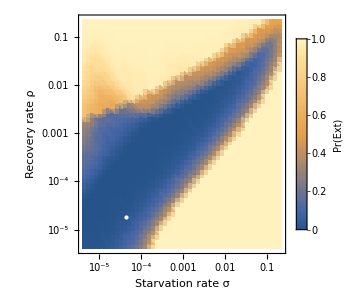

```mathematica
ExtPlot=Show[{
ListDensityPlot[MapAt[Log,Flatten[ExtinctionSigma,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(4*10^-6),Log@0.224},{Log@(4*10^-6),Log@(0.224)}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}]}]
}]
```

```mathematica
{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}
```

{Log[-(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19])],Log[-(1.67857×10^-6)/(M^(1/4) Log[0.292893/(1-0.707107 (1-0.0202 M^0.19)^(1/4))])]}

```mathematica
Starvation
```

0.

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf",ExtPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf

```mathematica
threshold =(N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality})*0.2/.M->Mass
```

16.6738

```mathematica
Mass
```

10

```mathematica
ts=Table[t,{t,0,100000000,100000}];
```

```mathematica
ts[[5]]
```

400000

```mathematica
ts[[1001]]
```

100000000

```mathematica
4*10^5
```

400000

```mathematica
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==4*10^(-6)},B,{n,1,50}]]
```

{4.×10^-6,5.×10^-6,6.25×10^-6,7.8125×10^-6,9.76563×10^-6,0.000012207,0.0000152588,0.0000190735,0.0000238419,0.0000298023,0.0000372529,0.0000465661,0.0000582077,0.0000727596,0.0000909495,0.000113687,0.000142109,0.000177636,0.000222045,0.000277556,0.000346945,0.000433681,0.000542101,0.000677626,0.000847033,0.00105879,0.00132349,0.00165436,0.00206795,0.00258494,0.00323117,0.00403897,0.00504871,0.00631089,0.00788861,0.00986076,0.012326,0.0154074,0.0192593,0.0240741,0.0300927,0.0376158,0.0470198,0.0587747,0.0734684,0.0918355,0.114794,0.143493,0.179366,0.224208}